```mathematica
ClearAll["Global`*"];
U[y_]:=((3 Cos[θ]^2-1)e2 L^2)/(2(r+y)^3);
dU=(U[y]+U[-y])/1-U[0];
dUg=(U[y]-U[-y])/2;
df=D[dU,{y,2}];
dg=D[dUg,{y,3}];
dh=D[dU,{y,4}];
y=0;
f=df;
g=dg;
h=dh;
Clear[y]
Print["Udd: "];
Print[dU]
Print["df: "];
Print[df];
Print["f: "];
Print[f];
Print["dg: "];
Print[dg];
Print["g: "];
Print[g];
Print["dh: "];
Print[dh];
Print["h: "];
Print[h];
```

Udd:

-(e2 L^2 (-1+3 Cos[θ]^2))/(2 r^3)+(e2 L^2 (-1+3 Cos[θ]^2))/(2 (r-y)^3)+(e2 L^2 (-1+3 Cos[θ]^2))/(2 (r+y)^3)

df:

(6 e2 L^2 (-1+3 Cos[θ]^2))/(r-y)^5+(6 e2 L^2 (-1+3 Cos[θ]^2))/(r+y)^5

f:

(12 e2 L^2 (-1+3 Cos[θ]^2))/r^5

dg:

1/2 (-(30 e2 L^2 (-1+3 Cos[θ]^2))/(r-y)^6-(30 e2 L^2 (-1+3 Cos[θ]^2))/(r+y)^6)

g:

-(30 e2 L^2 (-1+3 Cos[θ]^2))/r^6

dh:

(180 e2 L^2 (-1+3 Cos[θ]^2))/(r-y)^7+(180 e2 L^2 (-1+3 Cos[θ]^2))/(r+y)^7

h:

(360 e2 L^2 (-1+3 Cos[θ]^2))/r^7

```mathematica
ClearAll["Global`*"];
Do[
Clear[gx,b,bv,k];
Print["-------------------------------------------------------"];
Print["For ",i[[1]],": ",gx=i[[2]]];
g=(k-1)/k;

gg[k_]:=b/.Solve[gx==g,b][[2]];
Print["g[k]: ",bv=gg[k]];
(*Neturon data*)
(*E0=939.5654133;
Er=1/40*10^-6;
e2=1.43996427*^-13;
e1=4.80320425*^-10;

c=2.99792458*^10;
Edec=0.782;
µ= 9.66236*^-24;
S=1/2*6.582119569*^-22; *)
(*Pion data *)
(*E0=134.9766;
Er=1/40*10^-6; 
e2=1.43996427*^-13;
e1=4.80320425*^-10; 
c=2.99792458*^10;
Edec=0.782;
µ= k/2 e1 N0;
S=a*6.582119569*^-22;*)
(*Kaon data*)
E0=497.648;
Er=1/40*10^-6; 
e2=1.43996427*^-13;
e1=4.80320425*^-10; 
c=2.99792458*^10;
Edec=0.782;
µ= k/2 e1 N0;
S=a*6.582119569*^-22;
Print["N_0: ",N0=(S c)/E0];
Print["µ: ",µ];
(*Print["k: ",k=(2µ)/(e1 N0)];*)
Print["Ek: ",Ek=E0*(1-g)];
Print["Ep: ",Ep=E0-Ek];
Print["b: ",b=bv];
Print["r: ",r=(N0 k)/b];
Print["ω: ",ω=(b c)/r];
Print["f: ",f=(ω/c)^2 Er];
Print["L: ",l=e2/(E0 g-1/12 b^2 Er)];
Print["θ: ",θ=FullSimplify[ArcCos[√((f r^5)/(18e2 l^2)+1/3)]/° ],"°" ];
Print["x: ",x=Edec/(E0-Edec)];
Print["n: ",n=1/x];
Print["g: ",g=(30e2 l^2(3Cos[θ]-1))/r^6];
Print["h: ",h=(180e2 l^2(3Cos[θ]-1))/r^7];
tbl={};
Do[
Print["For k=",k,":"];
tb=Prepend[Table[{a=10^-j,k,µ,b,l,r,N0,f,g,h,θ},{j,Range[0,8]}],{"a","k","µ","b","l","r [cm]","N0 [cm]","f [MeV/cm^2]","g [MeV/cm^3]","h [MeV/cm^4]","θ"}];
AppendTo[tbl,tb];
Grid[tb,Frame->All]
,
{k,{2,5,10,20,50,100,200,500,1000}}
];
,
{i,{{"GM+",1/(1+b^2)}}}
];
```

-------------------------------------------------------

For GM+: 1/(1+b^2)

g[k]: 1/(√(-1+k))

N_0: 1.0501×10^-14

µ: 9.66236×10^-24

k: 3.83136

Ek: 245.23

Ep: 694.335

b: 0.594296

r: 6.76986×10^-14

ω: 2.63174×10^23

f: 1.92658×10^18

L: 2.07388×10^-16

θ: 54.7341°

x: 0.000832993

n: 1200.49

g: -3.32743×10^36

h: -2.94904×10^50

For k=2:

For k=5:

For k=10:

For k=20:

For k=50:

For k=100:

For k=200:

For k=500:

For k=1000:

```mathematica
939.5654133*1/3.8313577172019837*1/(2.99792458*^10)*0.594295756083999*6.769857485046848*^-14
```

3.29106×10^-22

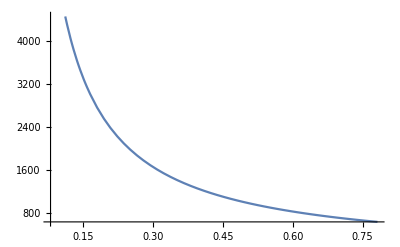

0.782 | 0.742 | 0.702 | 0.662 | 0.622 | 0.582 | 0.542 | 0.502 | 0.462 | 0.422 | 0.382 | 0.342 | 0.302 | 0.262 | 0.222 | 0.182 | 0.142 | 0.102
635.379 | 669.685 | 707.9 | 750.734 | 799.077 | 854.065 | 917.17 | 990.331 | 1076.16 | 1178.26 | 1301.74 | 1454.11 | 1646.84 | 1898.42 | 2240.66 | 2733.33 | 3503.56 | 4877.9

```mathematica
Plot[(E0-Ed)/Ed,{Ed,0.080,Edec}]
table=Append[{Range[Edec,0.080,-0.040]},Table[(E0-Ed)/Ed,{Ed,Edec,0.080,-0.040}]];
Grid[table,Frame->All]
```

```mathematica
N[ArcCos[√(1/3)]]/°
```

54.7356

```mathematica
Grid[tbl[[6]],Frame->All]
```

a | k | µ | b | l | r [cm] | N0 [cm] | f [MeV/cm^2] | g [MeV/cm^3] | h [MeV/cm^4] | θ
1 | 100 | 9.52281×10^-22 | 1/(3 √11) | 2.92277×10^-16 | 3.94532×10^-11 | 3.96519×10^-14 | 1.62234×10^11 | 1.77678×10^90+0. ⅈ | 2.70211×10^101+0. ⅈ | 0.+161.372 ⅈ
1/10 | 100 | 9.52281×10^-23 | 1/(3 √11) | 2.92277×10^-16 | 3.94532×10^-12 | 3.96519×10^-15 | 1.62234×10^13 | 1.82072×10^26 | 2.76893×10^38 | 50.5714
1/100 | 100 | 9.52281×10^-24 | 1/(3 √11) | 2.92277×10^-16 | 3.94532×10^-13 | 3.96519×10^-16 | 1.62234×10^15 | -1.69488×10^32 | -2.57756×10^45 | 54.7314
1/1000 | 100 | 9.52281×10^-25 | 1/(3 √11) | 2.92277×10^-16 | 3.94532×10^-14 | 3.96519×10^-17 | 1.62234×10^17 | -1.68277×10^38 | -2.55914×10^52 | 54.7356
1/10000 | 100 | 9.52281×10^-26 | 1/(3 √11) | 2.92277×10^-16 | 3.94532×10^-15 | 3.96519×10^-18 | 1.62234×10^19 | -1.68276×10^44 | -2.55913×10^59 | 54.7356
1/100000 | 100 | 9.52281×10^-27 | 1/(3 √11) | 2.92277×10^-16 | 3.94532×10^-16 | 3.96519×10^-19 | 1.62234×10^21 | -1.68276×10^50 | -2.55913×10^66 | 54.7356
1/1000000 | 100 | 9.52281×10^-28 | 1/(3 √11) | 2.92277×10^-16 | 3.94532×10^-17 | 3.96519×10^-20 | 1.62234×10^23 | -1.68276×10^56 | -2.55913×10^73 | 54.7356
1/10000000 | 100 | 9.52281×10^-29 | 1/(3 √11) | 2.92277×10^-16 | 3.94532×10^-18 | 3.96519×10^-21 | 1.62234×10^25 | -1.68276×10^62 | -2.55913×10^80 | 54.7356
1/100000000 | 100 | 9.52281×10^-30 | 1/(3 √11) | 2.92277×10^-16 | 3.94532×10^-19 | 3.96519×10^-22 | 1.62234×10^27 | -1.68276×10^68 | -2.55913×10^87 | 54.7356

```mathematica
z=6.76986/8.641
```

```mathematica
0.7834579331095939
```

0.783458

```mathematica
b=(2*9.66236*^-24)/(4.8032*^-10*8.641*^-14)
```

0.465606

```mathematica
(b^3*3.8313577172019837^2)/(1+b^2*3.8313577172019837^2)
```

0.354278

```mathematica
(3.291*^-22*2.997*^10*3.8313577172019837)/(8.641*^-14*939.565)
```

0.465454

```mathematica
(3.291*^-22*2.997*^10*4.8032*^-10)/(2*9.66236*^-24)
```

```mathematica
N[1/(√(1-0.4656059637285363^2))]
```

1.12995

```mathematica
245.15010621835654/(1.1299535392975943-1)
```

```mathematica
1886.444244176847/2
```

943.222

```mathematica
(245.15010621835654 √(1-0.4656059637285363^2))/(√(1-0.4656059637285363^2)-1)
```

-1886.44

```mathematica
1375.9741059616163-939.565
```

436.409

```mathematica
((1375.9741059616163-939.565)/245)^-1
```

0.5614

```mathematica
√((939.565-245)^2+(939.565+245)^2)
```

1373.18